# Análisis de datos idealista18

## David Recio Pastor

## Preprocesado de datos y anomalías

El set elegido para esta prueba ha sido el de la ciudad de Valencia. Importamos los datos descargados del repositorio de Github y empezamos el procesado de los datos.

Los datos tienen una dimensiones de 33622 filas y 46 columnas. Las descripciones de las columnas las encontramos en el paper “A geo-referenced micro-data set of real estate listings for the three largest Spanish cities from the Idealista website”.

Tras una primera observación de los datos, observamos que hay 4 períodos, los cuatro trimestres de 2018, que convertimos de numero entero a formato fecha por conveniencia. La primera acción que llevamos a cabo es agrupar por “ASSETID”, para ver si tenemos varias observaciones de un mismo ASSETID en diferentes períodos temporales. No es el caso, tenemos 4476 “ASSETID” con más de una observación pero todas en el mismo período. El número de observaciones por ASSETID tiene la siguiente distribución:

Dejamos a un lado lo que tienen 1 observación, y tratamos el resto. Para cada “ASSETID” con más de una observación, alistamos el resto de características, buscando si valores como precio, número de habitaciones u otros son iguales o difieren para un teóricamente mismo inmueble. Ponemos un ejemplo:

Como se observa, hay 3 valores de precio y dos de superficie. Su tuviésemos referencias temporales diarias, podríamos elegir la última por entender que el anuncio se puso incorrectamente y luego se corrigió pero, como no es el caso, la elección es descartar esta observación. La regla de decisión para descartar observaciones dudosas es la siguiente:

	- Para todas las características inmutables (superficie, terraza, ser duplex, orientacion, planta...) directamente descartamos las observaciones, ante la imposibilidad de conocer el valor real. Descartamos 826 ASSETID.
	- Cuando el único valor con más de una observación es el precio, tomamos el mínimo, entendiendo que es el último que se ha puesto y supone una rebaja.
	- Con respecto a la situación geográfica, para longitud o latitud hay 3650 observaciones con más de un valor. Para resolverlo, nos quedamos con la media de los valores que existan, al igual que para el resto de valores de distancias.
		
Hechas estas primeras correcciones, tenemos 26.555 filas. Hemos descartado 7067, un 21,02%.

Estos serían los descartes de filas, por el lado de las columnas o características, decidimos eliminar:

	- ADTYPOLOGYID, ADOPERATIONID, ADTYPOLOGY, ADOPERATION y CITYNAME porque no aportan nada al análsis.
	- PARKINGSPACEPRICE porque no tiene sentido, debería ser un rango de precios pero no son correctos, en la mayoría de casos el valor es 1.
	- De las variables HASPARKINGSPACE Y ISPARKINGSPACEINCLUDEDINPRICE nos deberiamos quedar con sólo una, ya que los valores son idénticos en ambas.
	- CONSTRUCTIONYEAR, el procedende del anunciante tiene 10533 obersaciones sin año, por lo que usamos el procedente del catastro.
	
El resto de variables pueden tener interés, aunque no usaremos todas en nuestro análisis.

## Estadística descriptiva

Tras la primera criba, empezamos con un análisis un poco más exhaustivo de nuestro dataset. Para ello, emplearemos diferentes métodos según características:

	- Para variables continuas, crearemos una tabla de medidas descriptivas de la muestra, además de un histograma y diagrama de caja para tener una idea visual de la distribución.
	- Para variables binarias, haremos un conteo y los pondremos de forma porcentual.
	- Para variable ordinales, contaremos la cantidad de sucesos de cada valor y descataremos para nuestro análisis global los menos relevantes (a nivel de generalizar).
	- Las coordenadas geográficas las usaremos para situar a cada inmueble en su barrio, incluyéndolo en un cluster de la ciudad para su posterior análisis gráfico.

### Variables continuas

#### PRICE - Precio absoluto

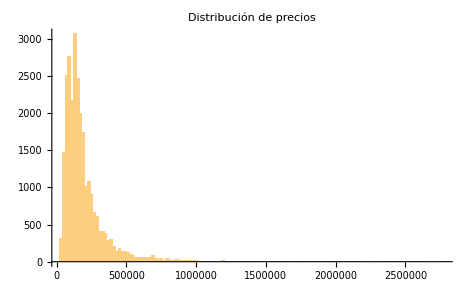
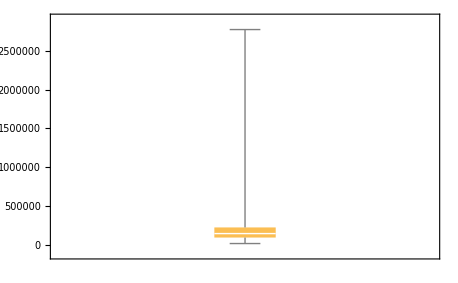

Vemos que hay valores atípicos que degeneran la distribución, produciendo una asimetría exagerada, podemos verlo en la diferencia entre media y mediana o, de forma aún más evidente, en los gráficos. Para solucionar este problema,  podríamos descartar valores por encima del top  1% o 5%.

Para este caso concreto, lo normal es usar la variable normalizada por superficie, “UNITPRICE”

#### UNITPRICE - Precio por metro

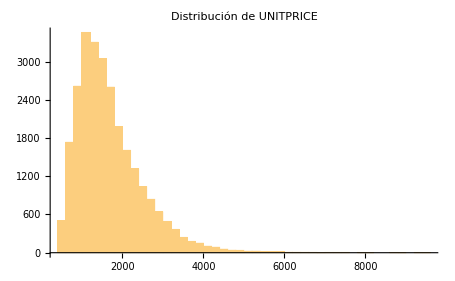
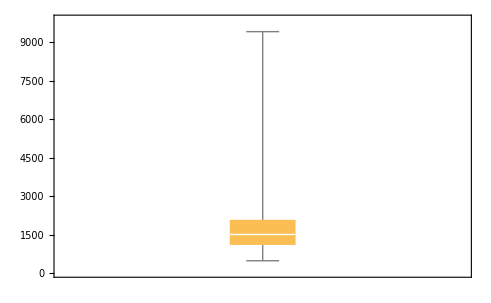

Como vemos, es mucho menos asimétrica, pero sigue teniendo algún valor atípico, ya que el máximo duplica su valor al top 1%, por lo que descartaremos las observaciones por encima de este top 1%.

#### CONSTRUCTED AREA

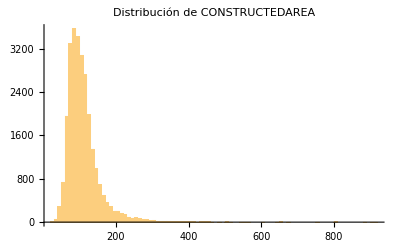

Como vemos, tiene una distribución similar a la de precio absoluto, pero con mayoir kurtosis, es decir, más concentración. Si eliminamos el último tanto por ciento de la muestra, nos quedaría una distribución mucho más simétrica, simplemente quitando un 1% de valores anómalos, que son 264 observaciones.

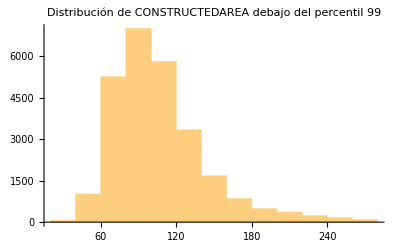

### Variables discretas y categóricas

#### Variables binarias

Se presenta la distribución de cada tipo como proporción sobre el total, por ejemplo, hay un 75,11% de viviendas sin terraza.

```mathematica
{{"HASTERRACE"->}, {"HASLIFT"->}, {"HASAIRCONDITIONING"->}, {"HASPARKINGSPACE"->}, {"HASBOXROOM"->}, {"HASWARDROBE"->}, {"HASSWIMMINGPOOL"->}, {"HASDOORMAN"->}, {"HASGARDEN"->}, {"ISDUPLEX"->}, {"ISSTUDIO"->}, {"ISINTOPFLOOR"->}}
```

#### Variables ordinales y categóricas

#### ROOMNUMBER

Agrupando las viviendas por número de habitaciones observamos que hay varios valores atípicos, un caso de una casa con 81 habitaciones que descartamos y varios valores que no van a tener ninguna relevancia a nivel de agrupación estadística. Por tanto, para nuestro estudio, vamos a quedarnos con las viviendas de 1 a 5 habitaciones.

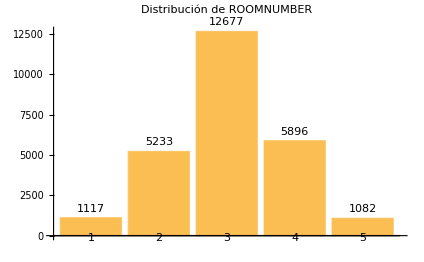
```mathematica
->         -Graphics-
```

#### BATHNUMBER

Usamos la misma metología y descartamos las viviendas con más de 3 baños y sin baños.

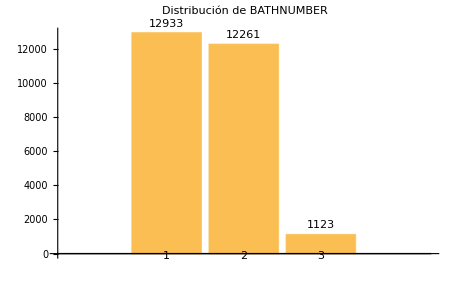
```mathematica
->         -Graphics-
```

#### AMENITYID

Contamos el número de viviendas de cada tipo, obervando que la gran mayoría de los inmuebles se venden amueblados por completo.

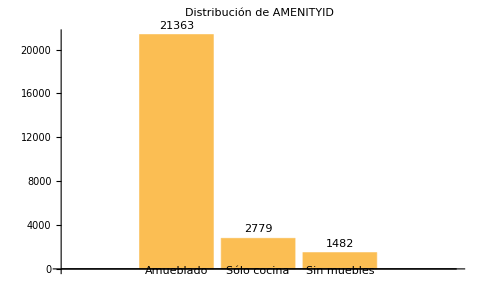

#### FLOORCLEAN

Esta variable indica la planta en la que se encuentra la vivienda, cabe mencionar que hay 1286 observaciones para las que no se tienen dato de planta, pero que no descartamos porque a priori no será una variable de diferenciación en nuestro modelo, pero si lo fuese deberían descartarse o aproximarse en función de la variable CADMAXBUILDINGFLOOR.

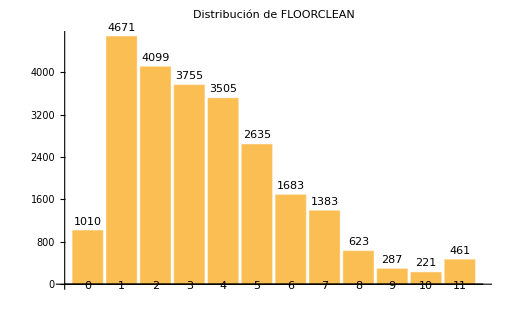

#### CADCONSTRUCTIONYEAR

Observar el año de construcción según el catastro es algo más curioso. Si hacemos una serie temporal agrupando número de viviendas por año construido vemos unas tendencias que podrían ser objeto de un estudio socioeconómico más profundo. Vemos que tenemos dos máximos locales en 1970 y en 2002 con 1213 y 416 viviendas respectivamente.

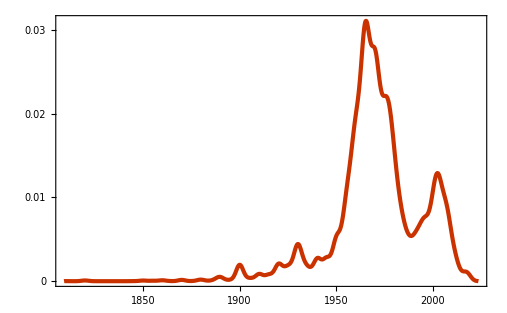

Habría más variables para analizar en este apartado, pero he decidido pasar al siguiente por la falta de tiempo por mi parte y porque entiendo que no es tan valioso.

### Variables geográficas o espaciales

Con los datos de coordenadas que tenemos, y usando los datos del archivo “Valencia_polygonds.csv” del repositorio de Github he hecho lo siguiente:

	- Para cada barrio, tengo su representación espacial dada por los vértices del polígono en el archivo mencionado.
	- Con las coordenadas de inmueble, calculo si un inmueble está dentro de un barrio o no.
	- Genero una nueva columna de mi dataset donde a cada inmueble le asigno el barrio al que pertenece.
	-  Hay 28 inmuebles que no están en ninguno de los barrios, estarían fuera de ciudad de acuerdo con nuestro polígonos.

#### Barrios con más anuncios

Como une ejemplo de uso de los datos espaciales, hemos tomado los barrios que más anuncios tienen:

#### Distribución espacial de las viviendas según año de construcción

Podemos observar que en la zona sur y noroeste es donde las viivendas son más nuevas y, evidentemente, tenemos la zona del centro historico como la zona donde las viviendas son más antiguas.

## Precios por segmentos

Como segmentación, vamos a tomar  el número de habitaciones, aunque siempre lo vamos a filtrar por barrio a la hora de visualizar, para tener esos dos ejes de diferenciación. Podríamos, en caso de tener más tiempo, hacerlo por orientación, podríamos tomar los puntos de interés y calcular precio de las viviendas en un radio de 100 metros/200 metros/300 metros... hay posibilidades casi ilimitadas.

### Número de habitaciones

Para generar los siguientes gráficos, el procedimiento que se ha seguido es el siguiente:
	
	- Filtrar el dataset por número de vivienda, obteniendo 5 subsets.
	- En cada subset, agrupar por barrio.
	- Calcular por el precio medio absoluto y asignarle ese valor a cada barrio.
	- Calcular el precio medio por metro cuadrado y asignarle ese valor a cada barrio.
	
Como enlace entre los dos, he creado este mapa de la media de metros por vivienda por barrio:

-Graphics-
El resultado muestral es el siguiente:

#### Viviendas de 1 habitación

#### Viviendas de 2 habitaciones

#### Viviendas de 3 habitaciones

#### Viviendas de 4 habitaciones

#### Viviendas de 5 habitaciones

Sin conocer Valencia en profundidad, viendo estos datos podemos ver claramente que la zona centro es la más cara y a zona suroeste la más humilde para viviendas de todos los tamaños. Tenemos huecos vacíos en zonas porque no tenemos datos para todas las zonas y todos los tipos de vivienda.

## Productos de datos y limitaciones

En mi opinión, la principal limitación de estos datos es la temporal. El mercado inmobiliario tiene como principal característica tener una reacción lenta ante los shocks externos. Sin duda, hay una parte del mercado que son inversiones a corto plazo (reforma y venta) pero en la mayoría de los casos este sector de la economía tiene un carácter largoplazista que hace que sus fluctuaciones en los precios sean mucho más lentas, aparte de verse habitualmente limitadas por medidas políticas ( en el contexto actual, modificaciones hipotecarias a préstamos variables, moratorias en otros casos...). En un mercado corriente, un aumento del precio real de la vivienda (por la subida de los precios de la financiaón), debería producir una rebaja en el precio nominal, pero esto no es algo que ocurra a corto plazo, por lo que no se puede analizar con datos anuales.

Como conclusión, una lista de ejemplo de productos y servicios que se podrían vender a partir de estos datos serían:

	- Pasar de datos de barrios a nivel de calles y cruzarlos con datos de renta per cápita por calles disponibles para ver la relación entre precio de vivienda y renta.
	
	- Evolución de las zonas en las que ha habido más anuncios de viviendas (y, como consecuencia, más actividad) a lo largo del tiempo para intentar anticipar tendencias en zonas “de moda” para que inmobiliarias puedan centrar su actividad.
	
	- No sé cómo se hace en idealista, pero creo que es muy importante tener información veraz sobre fecha de inicio de la venta, fecha en la que se realiza la operación y precio real. Se debe incentivar a los anunciantes a proporcionar esta información para ofrecer servicios más precisos y atractivos a los clientes de la plataforma.
	
	- Estimar el porcentaje real de operaciones que se realizan gracias/a través de idealista sobre el total de transmisiones reales (dato público) para tener una medida objetiva sobre el impacto de la plataforma sobre la que ejercer acciones de negocio.
	
	- Hacer un filtrado de viviendas por calidad de materiales/construcción basado en el análisis de las fotografías aportadas (con métodos de image identification entrenados para reconocer materiales, defectos estructurales... y también por zonas para poder conocer los edificios) para poder ordenar viviendas de más necesitadas de reformas a nuevas y poder vender este producto a empresas de reformas que pudieran oferecer sus servicios a anunciantes a través de idealista.